# Quad Prog min 0.5 x.G.x+c.x A_e.x=b_e and A_i.x≥b_i

## 16.6 Interior Point method Implementation Algorithm 16.4 p484/506 min 0.5 x.G.x+c.x A.x≥b

Initialize with feasible point (x_0,y_0,λ_0) i.e. y_0=A.x_0-b≥0_n and λ_0≥0_n

Iterate “to convergence” k=0,1,2,3,…

(x,y,λ)=(x_k,y_k,λ_k) and solve (16.58) with σ=0 to get (Δx^aff,Δy^aff,Δλ^aff).

Calculate μ=(y.λ)/m

Calculate (α̂)_aff=Max[0≤a≤1: (y,λ)+α(Δy^aff,Δλ^aff)≥0]

Calculate μ_aff=((y +  (α̂)_aff Δy^aff).(λ + (α̂)_aff Δλ^aff))/m

Set σ=(μ_aff/μ)^3

Solve 16.67 for (Δx,Δy,Δλ)

Choose τ_k∈(0,1) and set α̂=min(α_τ_k^pri,α_τ_k^dual) (see 16.66)

Update (x_k,y_k,λ_k)=(x_k,y_k,λ_k)+α̂(Δx,Δy,Δλ)

There is quite a lot of stuff to be defined and explained here! First
	(16.58) (G | 0 | -Aᵀ
A | -I | 0
0 | Λ | Y).(Δx
Δy
Δλ)=(-r_d
-r_p
-Λ.Y.e+σ μ e)=(-(G.x-Aᵀ.λ+c)
-(A.x-y-b))
-Λ.Y.e+σ μ e)
is just the Newton step.  Step 2.2 just estimates how far from “complementarity” the original point is. Step 2.3 works out how far you can go in the affine “Newton” direction and maintain feasibility.  Step 2.4 checks how far from “complementarity” the new trial point is.  Step 2.5 computes a new value for σ from the two complementarity gaps. Step 2.6 uses that σ in the Newton Step with the affine Λ and Y
	(16.67) (G | 0 | -Aᵀ
A | -I | 0
0 | Λ | Y).(Δx
Δy
Δλ)=(-r_d
-r_p
-(Λ.Y+ΔΛ^aff ΔY^aff)e+σ μ e)=(-(G.x-Aᵀ.λ+c)
-(A.x-y-b))
-(Λ.Y+ΔΛ^aff ΔY^aff)e+σ μ e)
Step 2.7 chooses maximum primal and dual steps sizes with the same safety factor τ
	(16.66) 	 α_τ^pri | = | Max[0≤α≤1:y+α Δy≥(1-τ)y]
α_τ^dual | = | Max[0≤α≤1:λ+α Δλ≥(1-τ)λ]
The Min ensures that both the updated slack variables y and updated Lagrange multipliers λ satisfy the feasibility conditions y+α̂ Δy≥0 and λ+α̂ Δλ≥0.  All of this manipulation is motivated by experience in the linear programming case and is designed to ensure that the “Newton” steps maintain feasibility.

Here are my code building blocks

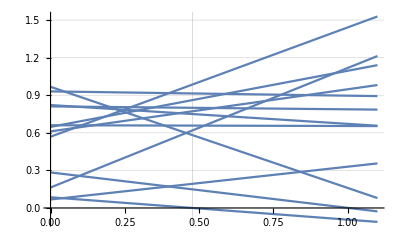

```mathematica
n=12;
ys=RandomReal[{0,1}, n];
Δys=RandomReal[{-1, 1}, n];
τ=1;
αTest=αStepComp[ys,Δys,τ];
Plot[ ys + α Δys,{α,0, 1.1},
GridLines->{{αTest}, Automatic}]
```

```mathematica
(* Generic Matrix *)
NewtonMatrix[G_,A_,λ_,y_]:= Module[{m=Length[G],n=Length[λ]},
ArrayFlatten[({{G, 0, -Aᵀ}, {A, -IdentityMatrix[n], 0}, {0, DiagonalMatrix[λ], DiagonalMatrix[y]}})]
]
(* Two different right hand sides for 11.58 and 11.67 *)
RHS58[G_,x_,A_,λ_,c_,y_,b_,σ_,μ_]:=Join[ -(G.x-Aᵀ.λ+c),-(A.x-y-b),-λ*y+σ μ]
RHS67[{G_,x_,A_,λ_,c_,y_,b_,σ_,μ_},{ΔλAff_,ΔyAff_}]:=RHS58[G,x,A,λ+ΔλAff,c,y+ΔyAff,b,σ,μ]
(* maximum feasible step *)
αStepComp[y_,Δy_,τ_]:=Module[{αs=-τ y/Δy},
αs=Select[αs, #>0&];
Min[1,Min[αs]]
]
```

Build out the iteration manually.

```mathematica
{m,n}={6,3};
(* Test problem for objective *)
G=RandomReal[{-1,1},{m,m}];G=G+Gᵀ;
c=RandomReal[{-1,1},m];
(* test problem for constraints *)
A=RandomReal[{-1,1},{n,m}];
b=RandomReal[{-1,-0.01},n];
```

```mathematica
(* Simple feasible Initial Conditions *)
(* By construction the origin is feasible *)
x0=0*c;
λ0=ConstantArray[1,n];
y0=A.x0-b;
(* Initialize iteration variables *)
{x,λ,y}={x0,λ0,y0};
(* compute feasibility gap *)
μ=(y.λ)/m;
(* Construct Newton Matrix *)
NMat=NewtonMatrix[G,A,λ,y];
(* Compute Affine Step *)
σ=0.0;
RHSA = RHS58[G,x,A,λ,c,y,b,σ,μ];
ΔxΔλΔyA=LinearSolve[NMat,RHSA];
{ΔxA,ΔλA,ΔyA}={ΔxΔλΔyA⟦1;;m⟧,ΔxΔλΔyA⟦m+1;;m+n⟧,ΔxΔλΔyA⟦m+n+1;;m+2n⟧};
(* Compute max feasible Affine Step length *)
(* full step τ=1 *)
τ=1.0;
αHatA=αStepComp[Join[λ,y],Join[ΔλA,ΔyA],τ];
(* Update centering parameter σ *)
μA=(y+αHatA*ΔyA).(λ+αHatA*ΔλA)/m;
σ=(μA/μ)^3;
(* Solve 16.67 *)
RHS = RHS67[{G,x,A,λ,c,y,b,σ,μ},{ΔλA,ΔyA}];
ΔxΔλΔy=LinearSolve[NMat,RHS];
{Δx,Δλ,Δy}={ΔxΔλΔy⟦1;;m⟧,ΔxΔλΔy⟦m+1;;m+n⟧,ΔxΔλΔy⟦m+n+1;;m+2n⟧};
(* Compute max step lengths *)
(* safety factor 0<τ<1 *)
τ=0.9;
αPri=αStepComp[y,Δy,τ];
αDual=αStepComp[λ,Δλ,τ];
αHat=Min[αPri,αDual];
(* Update with step size αHat *)
{x,λ,y}={x,λ,y}+αHat{Δx,Δλ,Δy}
```

{{0.00294991,0.00901117,0.123434,-0.0243942,-0.0811844,0.0575582},{1.12756,1.18252,1.07548},{0.0120028,0.305175,0.484164}}

Build stepper function from script above.

```mathematica
InteriorPointStepper[{G_,c_},{A_,b_}][{x_,λ_,y_}]:= Module[
{m=Length[c],n=Length[b],μ, NMat,σ,RHSA,ΔxΔλΔyA,ΔxA,ΔλA,ΔyA,τ,
αHatA,μA,RHS,ΔxΔλΔy,Δx,Δλ,Δy,αPri,αDual,αHat},
(* compute feasibility gap *)
μ=(y.λ)/m;
(* Construct Newton Matrix *)
NMat=NewtonMatrix[G,A,λ,y];
(* Compute Affine Step *)
σ=0.0;
RHSA = RHS58[G,x,A,λ,c,y,b,σ,μ];
ΔxΔλΔyA=LinearSolve[NMat,RHSA];
{ΔxA,ΔλA,ΔyA}={ΔxΔλΔyA⟦1;;m⟧,ΔxΔλΔyA⟦m+1;;m+n⟧,ΔxΔλΔyA⟦m+n+1;;m+2n⟧};
(* Compute max feasible Affine Step length *)
(* full step τ=1 *)
τ=1.0;
αHatA=αStepComp[Join[λ,y],Join[ΔλA,ΔyA],τ];
(* Update centering parameter σ *)
μA=(y+αHatA*ΔyA).(λ+αHatA*ΔλA)/m;
σ=(μA/μ)^3;
(* Solve 16.67 *)
RHS = RHS67[{G,x,A,λ,c,y,b,σ,μ},{ΔλA,ΔyA}];
ΔxΔλΔy=LinearSolve[NMat,RHS];
{Δx,Δλ,Δy}={ΔxΔλΔy⟦1;;m⟧,ΔxΔλΔy⟦m+1;;m+n⟧,ΔxΔλΔy⟦m+n+1;;m+2n⟧};
(* Compute max step lengths *)
(* safety factor 0<τ<1 *)
τ=0.9;
αPri=αStepComp[y,Δy,τ];
αDual=αStepComp[λ,Δλ,τ];
αHat=Min[αPri,αDual];
(* Update with step size αHat *)
{x,λ,y}+αHat{Δx,Δλ,Δy}
]
```

Test some steps

```mathematica
{m,n}={6,3};
(* Test problem for objective *)
G=RandomReal[{-1,1},{m,m}];G=G+Gᵀ;
c=RandomReal[{-1,1},m];
(* test problem for constraints *)
A=RandomReal[{-1,1},{n,m}];
b=RandomReal[{-1,-0.01},n];
(* Simple feasible Initial Conditions. By construction the origin is feasible *)
{x,λ,y}={0*c,ConstantArray[1,n],-b};
(* Take some steps *)
MaxIter=6;
xλyData=Table[
{x,λ,y}=InteriorPointStepper[{G,c},{A,b}][{x,λ,y}],
{MaxIter}];
TabView[Map[MatrixPlot[#,PlotLegends->Automatic,FrameLabel->{"Iteration",None}]&,xλyDataᵀ]]
TabView[Map[MatrixForm,xλyDataᵀ]]
```

123

123

Test residuals

```mathematica
{x,λ,y}=xλyData⟦-1⟧;
{y,A.x-b}
```

{{2.29054,1.01186,0.187641},{-0.0394968,0.331803,0.644553}}